# Hodgkin-Huxley Nerve Model

## NDSolve Version

```mathematica
ClearAll[U,t,soln]
const = {Subscript[g, Na]=120.,Subscript[g, k]=36.,Subscript[g, L]=0.3,Subscript[V, 0]=-61.,Subscript[V, Na]=50.,Subscript[V, k]=-77.,Subscript[V, L]=-54.4,c=.01};
inits={n[0]==0.31,m[0]==.05,h[0]==.6,V[0]==Subscript[V, 0]};
Subscript[α, n][V_]:=(0.01*(V+.55))/Exp[(55+V)/10-1];
Subscript[α, m][V_]:=(0.1*(V+.40))/Exp[(40+V)/10-1];
Subscript[α, h][V_]:=0.07*Exp[(V+.65)/20];
Subscript[β, n][V_]:=0.125*Exp[(V+65)/80];
Subscript[β, m][V_]:=4.*Exp[(V+.65)/18];
Subscript[β, h][V_]:=1/Exp[(35+V)/10+1];
Subscript[j, A][t_]:=Which[5≤t<5.2,-5,7≤ t< 0,0,True,0];
tmax=0.5;
solnV=NDSolve[{V'[t]==(Subscript[j, A][t]-(Subscript[g, k]*n[t]^4*(V[t]-Subscript[V, k]))-(Subscript[g, Na]* m[t]^3*h[t]*(V[t]-Subscript[V, Na]))-(Subscript[g, L]*(V[t]-Subscript[V, L])))/c,
n'[t]==Subscript[α, n][V[t]]*(1-n[t])-Subscript[β, n][V[t]]*n[t],
m'[t]==Subscript[α, m][V[t]]*(1-m[t])-Subscript[β, m][V[t]]*m[t],
h'[t]==Subscript[α, h][V[t]]*(1-h[t])-Subscript[β, h][V[t]]*h[t],n[0]==.31,m[0]==.05,h[0]==.6,V[0]==Subscript[V, 0]},{V,n,m,h},{t,0,tmax}]⟦1,1,2⟧;
solnn=NDSolve[{V'[t]==(Subscript[j, A][t]-(Subscript[g, k]*n[t]^4*(V[t]-Subscript[V, k]))-(Subscript[g, Na]* m[t]^3*h[t]*(V[t]-Subscript[V, Na]))-(Subscript[g, L]*(V[t]-Subscript[V, L])))/c,
n'[t]==Subscript[α, n][V[t]]*(1-n[t])-Subscript[β, n][V[t]]*n[t],
m'[t]==Subscript[α, m][V[t]]*(1-m[t])-Subscript[β, m][V[t]]*m[t],
h'[t]==Subscript[α, h][V[t]]*(1-h[t])-Subscript[β, h][V[t]]*h[t],n[0]==.31,m[0]==.05,h[0]==.6,V[0]==Subscript[V, 0]},{V,n,m,h},{t,0,tmax}]⟦1,2,2⟧;
solnm=NDSolve[{V'[t]==(Subscript[j, A][t]-(Subscript[g, k]*n[t]^4*(V[t]-Subscript[V, k]))-(Subscript[g, Na]* m[t]^3*h[t]*(V[t]-Subscript[V, Na]))-(Subscript[g, L]*(V[t]-Subscript[V, L])))/c,
n'[t]==Subscript[α, n][V[t]]*(1-n[t])-Subscript[β, n][V[t]]*n[t],
m'[t]==Subscript[α, m][V[t]]*(1-m[t])-Subscript[β, m][V[t]]*m[t],
h'[t]==Subscript[α, h][V[t]]*(1-h[t])-Subscript[β, h][V[t]]*h[t],n[0]==.31,m[0]==.05,h[0]==.6,V[0]==Subscript[V, 0]},{V,n,m,h},{t,0,tmax}]⟦1,3,2⟧;
solnh=NDSolve[{V'[t]==(Subscript[j, A][t]-(Subscript[g, k]*n[t]^4*(V[t]-Subscript[V, k]))-(Subscript[g, Na]* m[t]^3*h[t]*(V[t]-Subscript[V, Na]))-(Subscript[g, L]*(V[t]-Subscript[V, L])))/c,
n'[t]==Subscript[α, n][V[t]]*(1-n[t])-Subscript[β, n][V[t]]*n[t],
m'[t]==Subscript[α, m][V[t]]*(1-m[t])-Subscript[β, m][V[t]]*m[t],
h'[t]==Subscript[α, h][V[t]]*(1-h[t])-Subscript[β, h][V[t]]*h[t],n[0]==.31,m[0]==.05,h[0]==.6,V[0]==Subscript[V, 0]},{V,n,m,h},{t,0,tmax}]⟦1,4,2⟧;
VPlot= Plot[solnV[t],{t,0,tmax},PlotRange->All]
```

```mathematica
Table[Subscript[j, A][t],{t,0,30}]
```

# FiztHugh-Nagumo Nerve Model

## NDSolve Version

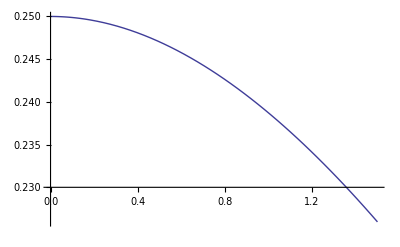

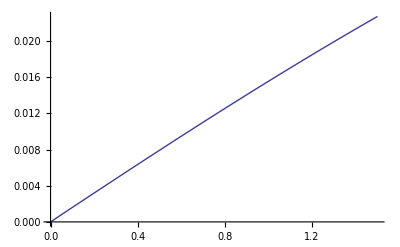

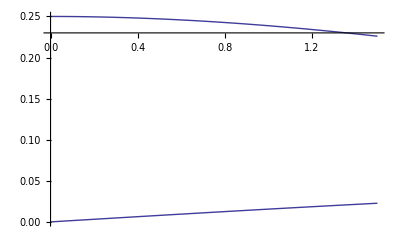

```mathematica
ClearAll[eqs,vars,const,t,tmax,soln]
const = {Subscript[I, A]=0.0,α=0.25,β=.1,γ=.1,tmax=1.5};
solnV=NDSolve[{V'[t]==(-V[t] *((α-V[t] )*(V[t]-1.)) )- W[t] + Subscript[I, A],W'[t]==β*V[t]-(γ*W[t]),V[0]==0.25,W[0]==0.0},{V,W},{t,0,tmax}]⟦1,1,2⟧;
solnW=NDSolve[{V'[t]==-V[t] *((α-V[t] )*(V[t]-1.)) - W[t] + Subscript[I, A],W'[t]==β*V[t]-(γ*W[t]),V[0]==0.16,W[0]==0.0},{V,W},{t,0,tmax}]⟦1,2,2⟧;
VPlot=Plot[solnV[t],{t,0,tmax},PlotRange->All]
WPlot=Plot[solnW[t],{t,0,tmax},PlotRange->All]
Show[VPlot,WPlot]
```

# FitzHugh-Nagumo Nerve Model, Mk.II

## NDSolve Version

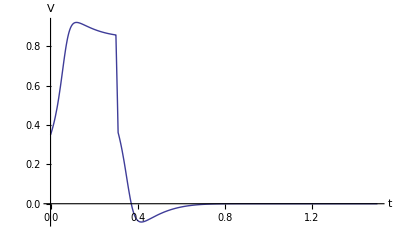

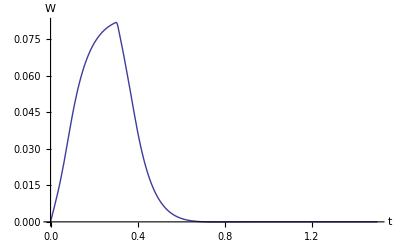

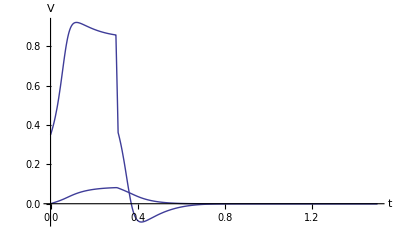

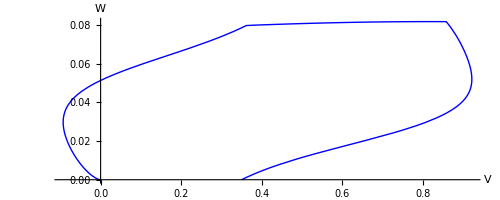

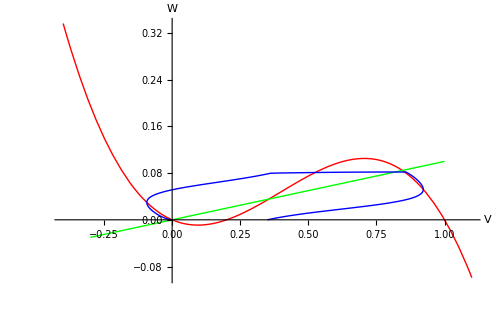

```mathematica
ClearAll[eqs,vars,const,params,tmax,soln,i,v,w]
eqs={V'[t]==(-V[t]*(V[t]-α)*(V[t]-1.) - W[t] + i[t])/ϵ,W'[t]==β*V[t] - γ*W[t],V[0]==0.35,W[0]==0.00};
vars={V[t],W[t]};
(*i=0.0;*)
γ=10.0;
β=1.0;
α=0.2;
ϵ=0.01;
tmax=1.5;
i[t_]:=Which[0.3≤t<0.31,-0.5,tmax≤ t< 0,0.0,True,0.0];
solnV=NDSolve[eqs,{V,W},{t,0,tmax}]⟦1,1,2⟧;
solnW=NDSolve[eqs,{V,W},{t,0,tmax}]⟦1,2,2⟧;
VPlot=Plot[solnV[t],{t,0,tmax},PlotRange->All,AxesLabel->{t,V}]
WPlot=Plot[solnW[t],{t,0,tmax},PlotRange->All,AxesLabel->{t,W}]
Show[VPlot,WPlot]
NCPlot1=Plot[-(t*(t-α)*(t-1.))+i[0],{t,-.4,,.01,1.1},PlotRange->All,PlotStyle->Red];
NCPlot2=Plot[(β*t)/γ,{t,-.3,.01,1},PlotRange->All,PlotStyle->Green];
VList = ParametricPlot[{solnV[t],solnW[t]},{t,0,tmax},PlotRange->All,PlotStyle->Blue,AxesOrigin->{0,0},AxesLabel->{V,W}]
Show[NCPlot1,NCPlot2,VList,AxesLabel->{V,W},AxesOrigin->{0,0},ImageSize->500]
```

## Manipulate Form

```mathematica
Manipulate[Module[{solnV,solnW,eqs={V'[t]==(-V[t]*(V[t]-α)*(V[t]-1.) - W[t] + i[t])/ϵ,W'[t]==β*V[t] - γ*W[t],V[0]==Subscript[V, 0],W[0]==Subscript[W, 0]}},
i[t_]:=Which[1≤t<1.1,Subscript[i, 0],tmax≤ t< 0,Subscript[i, 0],True,Subscript[i, 0]];
solnV=NDSolve[eqs,{V,W},{t,0,tmax}]⟦1,1,2⟧;
solnW=NDSolve[eqs,{V,W},{t,0,tmax}]⟦1,2,2⟧;
VPlot=Plot[solnV[t],{t,0,tmax},PlotRange->All];
WPlot=Plot[solnW[t],{t,0,tmax},PlotRange->All];
NCPlot1=Plot[-(t*(t-α)*(t-1.))+Subscript[i, 0],{t,-.4,,.01,1.1},PlotRange->All,PlotStyle->Red];
NCPlot2=Plot[(β*t)/γ,{t,-.3,.01,1},PlotRange->All,PlotStyle->Green];
VWPlot=ParametricPlot[{solnV[t],solnW[t]},{t,0,tmax},PlotRange->All,PlotStyle->Blue];
Show[VPlot,WPlot,ImageSize->300,AxesLabel->{t,V}]
Show[NCPlot1,NCPlot2,VWPlot,ImageSize->500,AxesOrigin->{0,0},AxesLabel->{V,W}]
],
{{tmax,7.5},1,30,.5},{{α,0.2},0,5,.1},{{β,2.0},0,10.0,.1},{{γ,2.4},0,10.0,.1},{{ϵ,0.01},0.01,1.0,.1},{{Subscript[V, 0],0.25},-1,1,.05},{{Subscript[W, 0],0.0},0.0,1,.05},{{Subscript[i, 0],0.15},-1.,1.,0.05},ContinuousAction->True,ControlPlacement->Left
]
```

```mathematica
DynamicModule[{tmax=7.5,α=0.2,β=2.,γ=2.4,ϵ=0.01,$86=0.25,$87=0.,$88=0.15},Module[{solnV$,solnW$,eqs$={V'[t]==(-V[t] (V[t]-α) (V[t]-1.)-W[t]+i[t])/ϵ,W'[t]==β V[t]-γ W[t],V[0]==$86,W[0]==$87}},i[t$_]:=Which[1≤t$<1.1,$88,tmax≤t$<0,$88,True,$88];solnV$=NDSolve[eqs$,{V,W},{t,0,tmax}]⟦1,1,2⟧;solnW$=NDSolve[eqs$,{V,W},{t,0,tmax}]⟦1,2,2⟧;VPlot=Plot[solnV$[t],{t,0,tmax},PlotRange->All];WPlot=Plot[solnW$[t],{t,0,tmax},PlotRange->All];NCPlot1=Plot[-(t (t-α) (t-1.))+$88,{t,-0.4,Null,0.01,1.1},PlotRange->All,PlotStyle->Red];NCPlot2=Plot[(β t)/γ,{t,-0.3,0.01,1},PlotRange->All,PlotStyle->Green];VWPlot=ParametricPlot[{solnV$[t],solnW$[t]},{t,0,tmax},PlotRange->All,PlotStyle->Blue];Show[VPlot,WPlot,ImageSize->300] Show[NCPlot1,NCPlot2,VWPlot,ImageSize->500,AxesOrigin->{0,0}]]]
```

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

# Morris-Lecar Nerve Model

## NDSolve Version

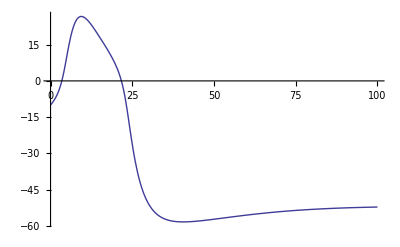

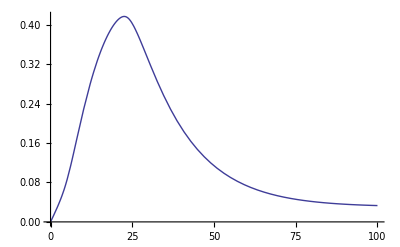

```mathematica
solnV=NDSolve[{V'[t]==(-2.2*(1.+Tanh[(V[t]+1)/15.])*(V[t]-100.) - 8*W[t]*(V[t]+70.) - 2*(V[t]+50.)+ 0.0)/20.0,W'[t]==0.020*Cosh[V[t]/60.]*(1.+Tanh[V[t]/30.] - 2.0*W[t]),V[0]==-10.0,W[0]==0.0},{V,W},{t,0,100}]⟦1,1,2⟧;
solnW=NDSolve[{V'[t]==(-2.2*(1.+Tanh[(V[t]+1)/15.])*(V[t]-100.) - 8*W[t]*(V[t]+70.) - 2*(V[t]+50.)+ 0.0)/20.0,W'[t]==0.020*Cosh[V[t]/60.]*(1.+Tanh[V[t]/30.] - 2.0*W[t]),V[0]==-10.0,W[0]==0.0},{V,W},{t,0,100}]⟦1,2,2⟧;
VPlot=Plot[solnV[t],{t,0,100},PlotRange->All]
WPlot=Plot[solnW[t],{t,0,100},PlotRange->All]
Show[VPlot,WPlot];
```